## 161Lu

```mathematica
ClearAll["Global`*"]
```

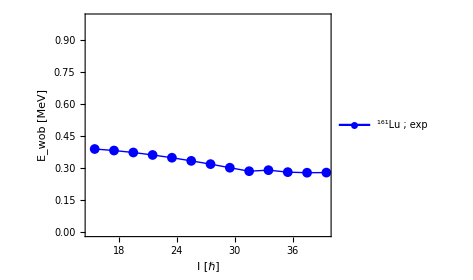

```mathematica
yrastEn=Sort[{13270.8,12139.8,11044.3,9985.5,8961.5,7964.1,6997.2,6072.8,5196.9,4373.1,3604.4,2893.8,2244.4,1658.6,1139.9,689.0,308.3,0}];
wob1En=Sort[{10794,9752,8744,7771,6820.6,5936.6,5103.6,4322.6,3597.6,2930.5,2324.5,1781.4,1303.7}];
yrastSpin=Table[i/2,{i,21,89,4}];
wob1Spin=Table[i/2,{i,31,79,4}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i+2]]+yrast[[i+3]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black},PlotLegends->Placed[{Style[Row[{Superscript["","161"],"Lu ; exp"}],30]},{0.4,0.85}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/161Lu.pdf",fig];
Show[fig]
```